# A Wolfram Framework for NFT Analytics

Kai Harris

The idea behind this project is to design a set of tools to help visualise and analyse NFT market behaviour . The marketplace  on [ https://opensea.io/ ] will be our testing - ground .
API: Function(s) that handle database interactions, usually in the context of networks. 
NFT: Type of contract on a Turing complete Blockchain.
CryptoPunks: Oldest collection of NFTs on the Ethereum blockchain.

## Designing an API

Here we look at the page [ https://docs.opensea.io/reference ] in order to learn how to create a fully functional set of API connectors between the local machine and the OpenSea Server, so that we can request data from their database and do analytics on it and then use wolfram in-builts to do explorations on the data.  Included are functions with examples on how to use them, and a larger more interesting example at the end of the chapter.

## API Function Parameters

To fully utilise the provided API framework, the following arguments will serve as reference material. These are all designated by the service provider, who is OpenSea, in this case.

Owner (String)  : The address of the owner of the Assets.

On-Sale (Bool) : If set to true, only show bundles currently on sale. If set to false, only show bundles that have been sold or cancelled.

Token Ids (String) : An array of token IDs to search for (e.g. ?token_ids=1&token_ids=209). Will return a list of assets with “token_id” matching any of the IDs in this array.

Asset Contract Address (String) : The NFT contract address for the assets.

Asset Contract Addresses (String) : An array of contract addresses to search for (e.g. ?asset_contract_addresses=0x1...&asset_contract_addresses=0x2...). Will return a list of assets with contracts matching any of the addresses in this array. If “token_ids” is also specified, then it will only return assets that match each (address, token_id) pairing, respecting order.

Order By (String) : How to order the assets returned. By default, the API returns the fastest ordering (contract address and token id). Options you can set are “token_id”, “sale_date” (the last sale’s transaction’s timestamp), “sale_count “(number of sales), “visitor_count” (number of unique visitors), and “sale_price” (the last sale’s total_price).

Order Direction (String) : Can be “asc” for ascending or “desc” for descending.

Offset (Int) : Return offset.

Limit (Int) : Return Limit.

Collection (String) : Limit responses to members of a collection. Case sensitive and must match the collection slug exactly. Will return all assets from all contracts in a collection. For more information on collections, see our collections documentation.

Event Type (String) : The event type to filter. Can be created for new auctions, successful for sales, cancelled, bid_entered, bid_withdrawn, transfer, or approve

Only Open-Sea (Bool) : Restrict to events on OpenSea auctions. Can be true or false.

AuctionType (String) : Filter by an auction type. Can be English for English Auctions, dutch for fixed-price and declining-price sell orders (Dutch Auctions), or min-price for CryptoPunks bidding auctions.

Occurred Before (Date-Time) : Only show events listed before this timestamp. Seconds since the Unix epoch.

Occurred After (Date-Time) : Only show events listed after this timestamp. Seconds since the Unix epoch.

X-API-Key:  Optional API key

## General Functions

### getAssets

#### Function

```mathematica
getAssets[owner_:None, tokenIds_:None, assetContractAddress_:None, assetContractAddresses_:None, orderBy_:None,orderDirection_:None, offset_:0, limit_:None, collection_:None]:=
ImportString[
FromCharacterCode[
URLRead[
HTTPRequest[
URLBuild[
"https://api.opensea.io/api/v1/assets",
{"owner"->owner,"token_ids"->tokenIds,"asset_contract_address"->assetContractAddress,"asset_contract_addresses"->assetContractAddresses,"order_by"->orderBy,"order_direction"->orderDirection,"offset"->offset,"limit"->limit,"collection"->collection}
//DeleteCases[_->None]]]]["BodyBytes"]],
"RawJSON"];
```

#### Example

```mathematica
guys = Dataset[getAssets["0x2349334b6c1ee1eaf11cbfad871570ccdf28440e", None, None, None, None,None,0, None, None]];
```

```mathematica
Table[Import[Normal[guys["assets"][All,"image_original_url"]][[i]]], {i, Length[Normal[guys["assets"][All,"image_original_url"]]]}];
```

### getBundles

#### Function

```mathematica
getBundles[onSale_, owner_, assetContractAddress_:None, assetContractAddresses_:None, tokenIds_, limit_:None,offset_:0]:=
ImportString[
FromCharacterCode[
URLRead[
HTTPRequest[
URLBuild[
"https://api.opensea.io/api/v1/bundles",
{"on_sale"->onSale,"owner"->owner,"asset_contract_addr~ess"->assetContractAddress,"asset_contract_addresses"->assetContractAddresses,"token_ids"->tokenIds,"limit"->limit, "offset"->offset}
//DeleteCases[_->None]]]]["BodyBytes"]],
"RawJSON"];
```

#### Example

```mathematica
guys = Dataset[getBundles[True, "0x15143f84c5c43f170569c97944ca33315fa0dabf", None,None, "2855", None,0]]
```

```mathematica
Table[AnimatedImage[Import[DeleteCases[Normal[guys["bundles"][All,"assets"][[1]][All, "image_original_url"]],Null][[i]]]],{i, 2}]
```

{,}

### getContract

#### Function

```mathematica
getContract[assetContractAddress_, APIKey_:None]:=
ImportString[
FromCharacterCode[
URLRead[
HTTPRequest[
URLBuild[
"https://api.opensea.io/api/v1/asset_contract/"<>assetContractAddress,
{"Accept"->"application/json", "X-API-KEY"->APIKey}
//DeleteCases[_->None]]]]
["BodyBytes"]],
"RawJSON"];
```

#### Example

With the collection of Cryptopunks, one of whome can be seen here [ https://opensea.io/assets/0xb47e3cd837ddf8e4c57f05d70ab865de6e193bbb/3350 ], we call the following function to get the contract data.

```mathematica
Dataset[getContract["0xb47e3cd837ddf8e4c57f05d70ab865de6e193bbb", None]];
```

### getEvents

#### Function

```mathematica
getEvents[assetContractAddress_, collectionSlug_:None, tokenID_:None, accountAddress_:None, eventType_:None,onlyOpensea_:None, auctionType_:None, offset_:0, limit_:None, occuredBefore_:None, occuredAfter_:None]:=
ImportString[
FromCharacterCode[
URLRead[
HTTPRequest[
URLBuild[
"https://api.opensea.io/api/v1/events",
{"asset_contract_address"-> assetContractAddress,"collection_slug"->collectionSlug,"token_id"->tokenID,"account_address"->accountAddress,"event_type"->eventType,"only_opensea"->onlyOpensea,"auction_type"->auctionType,"offset"->offset,"limit"->limit,"occurred_before"->occuredBefore,"occurred_after"->occuredAfter}
//DeleteCases[_->None]]]]
["BodyBytes"]],
"RawJSON"];
```

#### Example

getEvents requests the market transactions of an NFT: e.g the bids/trades/sales events of pieces such as [ https://opensea.io/assets/0x7920f98733b912772f89dbdd95e221bb7e6d058f/148 ].

```mathematica
assetContractAddress = "0x7920f98733b912772f89dbdd95e221bb7e6d058f";
```

```mathematica
eventsJson[assetAddress_] := 
getEvents[assetAddress,None, None,None,None,True];
```

```mathematica
getPrices[assetAddress_] := 
Table[
Dataset[
eventsJson[assetAddress]]["asset_events"][All, "bid_amount"][i],
{i,Length[Dataset[eventsJson[assetAddress]]["asset_events"][All, "bid_amount"]]}]//DeleteCases[Null];
```

```mathematica
prices= getPrices[assetContractAddress];
```

```mathematica
prices = Table[
Quantity[FromDigits[prices[[i]]], "Ethers"], 
{i, Length[prices]}]
```

{1/40 Ξ,1/10 Ξ,1/8 Ξ,1/40 Ξ}

### getCollections

#### Function

```mathematica
getCollections[assetOwner_, offset_:0, limit_:None]:=
ImportString[
FromCharacterCode[
URLRead[
HTTPRequest[
URLBuild[
"https://api.opensea.io/api/v1/collections",
{"asset_owner"->assetOwner,"offset"->offset,"limit"->limit}
//DeleteCases[_->None]]]]
["BodyBytes"]],
"RawJSON"];
```

#### Example

In this case, we want to look at the twitter handles of the creators associated with the collection of a particular set of assets.

```mathematica
address = "0x848fa9ec76391b94a83442170085f8ca863b1624";
```

```mathematica
twitterCreatorChannels[address_] :=
Dataset[getCollections[address, None, None]][All,"twitter_username"];
```

```mathematica
names = Normal[DeleteCases[twitterCreatorChannels[address],Null]]
```

{thecryptotrunks,punkscomic,BoredApeYC,natealexnft,rariblecom,GodsUnchained,megacryptopolis,superrare,larvalabs}

### getAsset

#### Function

```mathematica
getAsset[assetContractAddress_, tokenId_, accountAddress_:None]:=
ImportString[
FromCharacterCode[
URLRead[
HTTPRequest[
URLBuild[
"https://api.opensea.io/api/v1/asset/"<>assetContractAddress<>"/"<>tokenId,
{"account_address"->accountAddress}//DeleteCases[_->None]]]]["BodyBytes"]],
"RawJSON"];
```

#### Example

```mathematica
"0xb47e3cd837ddf8e4c57f05d70ab865de6e193bbb"
```

```mathematica
guy = Import[Dataset[getAsset["0xb47e3cd837ddf8e4c57f05d70ab865de6e193bbb", "7804",None]]["image_original_url"]];
```

-Graphics-

## Example - Twitter Analytics: Buzzwords

In the "getCollections" example, we found the twitter handles of various NFT minters. Lets take that a step further. It might be interesting to check out what the twitter crypto-space has on their mind. To do this, we parse the recent hashtags of all of  the above NFT minters in order to find an interesting word cloud that summarises the most uttered phrase from this subset of the twitter crypto space.

```mathematica
addresses = {"0xdf4c62f992ab29c3649db1fe65425c055b5c3913", "0x863cd7e3268ee72656d9ccddc80ed446a7837c69", "0x848fa9ec76391b94a83442170085f8ca863b1624", "0xc6b0562605d35ee710138402b878ffe6f2e23807","0x9f79e17a35bf290925191245e1a1b4510d457497"};
```

```mathematica
users = DeleteDuplicates[Flatten[Table[Normal[DeleteCases[Dataset[Normal[twitterCreatorChannels[i]]],Null]],{i, addresses}]]];
```

### Buzzword getter

```mathematica
twitter=ServiceConnect["Twitter","New"]
```

ServiceObject[…]

```mathematica
hashtags = Table[twitter["UserHashtags","Username"->users[[i]]],{i, Length[users]}];
```

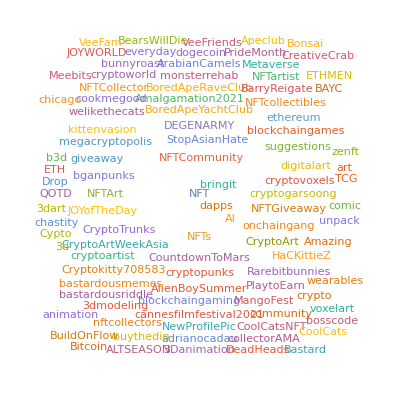

```mathematica
WordCloud[Flatten[hashtags]]
```

## Creating a CryptoPunk Database

Here we outline a process to create a set of large databases so we have local access to image data and trade data of the cryptopunks, who are a collection of 10000 NFTs. They are the original NFT’s on the Ethereum blockchain and so will serve as a good test-case for the  API functions. Included are some snapshots to show what each database looks like without having to download the files. If you would like to download the databases, they can be pulled from these addresses.

```mathematica
assetsDatabaseHyperlink = ["https://www.wolframcloud.com/obj/0.kai.rharris/Published/assetsFullOrdered.wl"](https://www.wolframcloud.com/obj/0.kai.rharris/Published/assetsFullOrdered.wl)
```

```mathematica
eventsDatabaseHyperlink = ["https://www.wolframcloud.com/obj/0.kai.rharris/Published/CleanFULLEventsOrdered.wl"](https://www.wolframcloud.com/obj/0.kai.rharris/Published/CleanFULLEventsOrdered.wl)
```

## Events

Below outlines a method to request large amounts of data from OpenSea via the getEvents API, and then parse it and clean it so that we can do analysis easily with Wolfram Language. This dataset will contain all trade data, including dates, prices, bids etc.

### Getting the Data

```mathematica
dir = DirectoryName["D:\\Wolfram"];
file=FileNameJoin[{dir,"eventsFULL.wl"}];

address = "0xb47e3cd837ddf8e4c57f05d70ab865de6e193bbb";
event = None;

PutAppend[
getEvents[address, None, 5001, None, event,False, None, 0,50],
file];

Table[
Pause[RandomInteger[{3,5}]];
PutAppend[getEvents[address, None, id, None, event,False, None, 0,50],file],{id,1,10000}];
```

### Loading the raw data

```mathematica
cryptopunksEventsDB=Import["D:\\eventsFULL.wl","ExpressionList"];
```

### Processing function

```mathematica
processCryptopunksEventsInformation[cryptopunk_]:=Module[
{
id=FromDigits[First[Lookup[Lookup[cryptopunk["asset_events"],"asset"],"token_id"]]]
},
id-> Function[u, <|"CreatedDate"-> u⟦1⟧,"CustomEventName"-> u⟦2⟧,"BidAmount"-> u⟦3⟧,"Duration"-> u⟦4⟧,"EndingPrice"-> u⟦5⟧,"EventType"-> u⟦6⟧,"PaymentToken"-> u⟦7⟧,"Seller"-> u⟦8⟧,"StartingPrice"-> u⟦9⟧,"TotalPrice"-> u⟦10⟧,"WinnerAccount"-> u⟦11⟧,"BlockHash"-> Lookup[u⟦12⟧,"block_hash"],"BlockNumber"-> Lookup[u⟦12⟧,"block_number"],"Timestamp"-> DateObject[Lookup[u⟦12⟧,"timestamp"]],"TXFromAddress"-> Lookup[u⟦12⟧,"from_account"]["address"],"TXToAddress"-> Lookup[u⟦12⟧,"to_account"]["address"],"TransactionHash"-> Lookup[u⟦12⟧,"transaction_hash"] |>]/@Lookup[cryptopunk["asset_events"],{"created_date","custom_event_name","bid_amount","duration","ending_price","event_type","payment_token","seller","starting_price","total_price","winner_account","transaction"}]
]
```

### Processing all the raw data

```mathematica
cryptopunksEvents=Association@(processCryptopunksEventsInformation/@DeleteCases[Flatten[cryptopunksEventsDB],<|"asset_events"->{}|>]);
```

### Sort and save the “clean” data

```mathematica
Put[KeySort[Dataset[cryptopunksEvents[[1]]]],"D:\\CleanFULLEventsOrdered.wl"]
```

### Test Data

```mathematica
events = Import["D:\\CleanFULLEventsOrdered.wl","ExpressionList"];
```

## Events Snapshot

A null event usually represents a rejected offer or a failed sale .

## Assets

Similarly, the following method requests and cleans the getAssets data from OpenSea. This database will contain information that includes hyperlinks to the image URLs.

### Getting the data

```mathematica
dir = DirectoryName["D:\\Wolfram"];
file=FileNameJoin[{dir,"assetsFULL.wl"}];
PutAppend[
getAssets[None, None, None,None, None,None, 0, 50, "cryptopunks"],
file];

Table[
Pause[RandomInteger[{5,10}]];
PutAppend[getAssets[None, None, None,None, None,None, 50, 50 + 50*x, "cryptopunks"],file],{x, 200}];
```

### Loading the raw data

```mathematica
cryptopunksAssetsDBFull=Import["D:\\assetsFULL.wl","ExpressionList"];
```

### Processing function

```mathematica
processCryptopunksAssetInformation[cryptopunk_]:=Function[u,FromDigits[u⟦1⟧]-> <|"TokenID"-> u⟦1⟧,"NumberOfSales"-> u⟦2⟧,"ImageURL"-> StringReplace[u⟦3⟧,"\n"-> ""],"ContractAddress"-> Lookup[u⟦4⟧,"address"],"CreationDate"-> DateObject[Lookup[u⟦4⟧,"created_date"]],"Name"-> u⟦5⟧,"ExternalLink"-> u⟦6⟧,"Owner"-> u⟦7⟧,"Traits"-> u⟦8⟧,"ImageOriginalURL"-> u⟦9⟧|>]@Lookup[cryptopunk,{"token_id","num_sales","image_url","asset_contract","name","external_link","owner","traits","image_original_url"}]
```

### Processing all the raw data

```mathematica
cryptopunkAssets=Association@(processCryptopunksAssetInformation/@Flatten[cryptopunksAssetsDBFull]);
```

### Sort and save clean data

```mathematica
Put[KeySort[cryptopunkAssets[[1]]],"D:\\assetsFULLOrdered.wl"];
```

### Test Data

```mathematica
assetsSaved = Import["D:\\assetsFULLOrdered.wl","ExpressionList"];
```

## Assets Snapshot

## Using the Database

Now that we have a large database we want to use it to represent the data in a human understandable way. The following chapter is all about exploring this data and trying to make sense out of it. Further explanations are included within.

## General NFT interest tracking over time

Using the events database, we can look at the market price fluctuations over the last few years.

### Extracting Time-Series Data

This loads the data into the notebook.

```mathematica
events = Import["D:\\CleanFULLEventsOrdered.wl","ExpressionList"];
eventsData = Dataset[events[[1]]];
```

This gets all corresponding events and bids from the database, and formats them.

```mathematica
bidOffered = ToExpression[Flatten[Table[Normal[eventsData[[i]][All, "BidAmount"]],{i, Length[eventsData]}]]];
eventsCreated = Flatten[Table[Normal[eventsData[[i]][All, "CreatedDate"]],{i, Length[eventsData]}]];
```

This cleans the Null trade data, and the corresponding event.

```mathematica
clean=With[{pos=Position[bidOffered,Null]},Delete[pos]/@{bidOffered,eventsCreated}];
```

This converts the bids and dates into correct price/time format , and puts it into DateListPlot format.

```mathematica
bids = CurrencyConvert[Quantity[clean[[1]], "Wei"],"Ethers"];
times = clean[[2]];
Activity = Table[{DateObject[times[[i]]], bids[[i]]}, {i,Length[bids]}];
```

### Visualisation

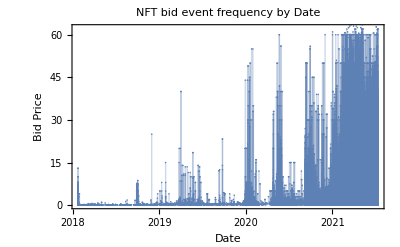

```mathematica
DateListPlot[Activity,Filling->Bottom,Joined->False,FrameLabel->{"Date", "Bid Price"}, PlotLabel->"NFT bid event frequency by Date"]
```

## Transaction graph: successful trades

We can think of the transaction between parties as a graph of nodes and edges, where the nodes are each party and the edges represent a transaction. Here we look at the cryptopunk transaction graphs as we increase the number of observed in the dataset.

#### Helper functions

Trades between accounts will be of the form:

```mathematica
sellers = {"addr1"};
buyers = {"addr_1"};
```

Where “addr{i}” and “addr_{i}” have transacted, so the following functions will create an interesting graph of trade activity:

```mathematica
connectionFunc[from_, to_] := from <-> to;
```

```mathematica
graphFunc[fromList_, toList_] :=  Graph[Table[ connectionFunc[fromList[[x]], toList[[x]]], {x,  Length[fromList]}]];
```

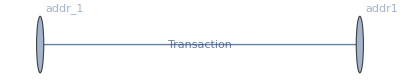

```mathematica
Graph[graphFunc[sellers, buyers], EdgeLabels->"Transaction", VertexLabels->{"addr1"->"addr1", "addr_1"->"addr_1"}]
```

#### Transaction correspondence

As an example, we load events into the notebook, and look at the first 100 data-points.

```mathematica
events = Import["D:\\CleanFULLEventsOrdered.wl","ExpressionList"];
events = Dataset[events][[1]];
dataSize= 400;
```

Format the corresponding seller and buyer data-points and separate them into arrays.

```mathematica
sellerEvents = Flatten[Table[Normal[events[[i]][All,"Seller"]],{i, dataSize}]];
buyerEvents = Flatten[Table[Normal[events[[i]][All,"WinnerAccount"]],{i, dataSize}]];
```

Remove null trades from the seller events, and remove corresponding buyer entries.

```mathematica
out=With[{pos=Position[sellerEvents,Null,{1}]},Delete[pos]/@{sellerEvents,buyerEvents}];
```

Separate seller and buyers into their own arrays.

```mathematica
sellers = Dataset[out[[1]]][All,"address"];
buyers = Dataset[out[[2]]][All,"address"];
```

Remove null addresses from buyer array, and corresponding sellers items.

```mathematica
out=With[{pos=Position[buyers,"0x0000000000000000000000000000000000000000",{1}]},Delete[pos]/@{buyers,sellers}];
```

Format output, separate into arrays.

```mathematica
sellers = Normal[out[[1]]];
buyers = Normal[out[[2]]];
```

#### Visualisation

```mathematica
Using
```

```mathematica
Graph[graphFunc[sellers, buyers], PlotLabel->StringInsert["Network with  Transactions",ToString[dataSize ],14]]
```

With

```mathematica
dataSize = {100, 200, 400, 800, 1600, 3600,6400}
```

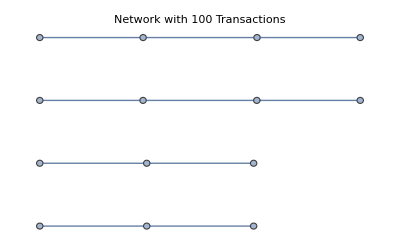
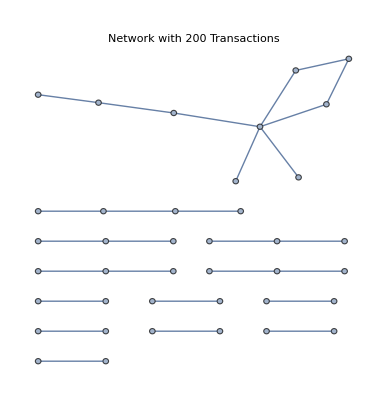
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

Note : we see that in these networks, the cleaning process removes many of the irrelevant data-points, and doubly linked nodes represent multiple trades between the same two parties.

## Machine Learning: price prediction based on image composition

Not all crypto punks have been sold or bid for yet. The idea here is to look at the ones that have had interest and find the average price of the punk. Using this information, we create an association between the cryptopunks images and their average bid, and train a model, which we use to predict the market value of an unsold cryptopunk based on its image composition.

### Pre-Process Prices

Load events database into notebook.

```mathematica
events = Import["D:\\CleanFULLEventsOrdered.wl","ExpressionList"];
eventData = Dataset[events[[1]]];
```

Pick dataset size to work with, and take this many items from the database.

```mathematica
dataSize = 100;
eventsTake= Take[eventData, dataSize];
```

Find the ids of each punk in the current database.

```mathematica
punkIDs = Normal[Keys[eventsTake]];
```

For each punk, look at the trading events and create a list of the mean trade price. Ignore null trades.

```mathematica
bidMeans = Table[Mean[ToExpression[DeleteCases[Normal[eventsTake[[i]][All, "BidAmount"]], Null]]], {i,dataSize }];
```

Look at the positions of the bid data where there have been no bids/sales etc. These will be the items we want to predict the market value of.

```mathematica
testPos = Flatten[Position[bidMeans, Mean[{}]]];
```

Create a set of data complementary to this. This is the set of items which we will train the model on.

```mathematica
trainingPos = Complement[Range[dataSize], Flatten[testPos]];
```

Loop through the training positions, and find the corresponding ids.

```mathematica
trainingIDs = Table[punkIDs[[i]], {i, trainingPos}];
```

Use the training ids to locate the testing ids.

```mathematica
testIDs = Complement[punkIDs,trainingIDs];
```

### Pre-Process Images

Load image data into the notebook.

```mathematica
cryptopunksAssetsDB = Import["D:\\assetsFullOrdered.wl","ExpressionList"];
imageURLs = cryptopunksAssetsDB[[1]][All, "ImageOriginalURL"];
```

### Train and Predict

#### Training

Create a correspondence between images by training id, and training bid prices. Train the model.

```mathematica
trainingSet = Table[Import[Normal[imageURLs[[punkIDs[[i]]+1]]]]-> bidMeans[[i]],{i, trainingPos}];
```

```mathematica
imageClassification = Predict[trainingSet]
```

PredictorFunction[…]

#### Testing

Import a unsold punk, and estimate its price.

```mathematica
testPunk = Import[imageURLs[[testPos[[8]]]]]
```

```mathematica
estimate  = Quantity[imageClassification[testPunk],"Wei"];
```

```mathematica
estimate  = Quantity[imageClassification[testPunk],"Ethers"];
```

17.0535 Ξ

## Wider Scope

The NFT space is young, born in 2017. Who knows where it will go. In terms of this project, here are some thoughts about the future of the tech.

## Whats next?

#### Index Tracker

A useful extension of this project would be an interactive index tracker using dynamic market data.This could  then be utilised in some sort of an NFT exchange hub.Of course, the bottle  neck is the speed of Ethereum network transactions. As blockchains become more optimised, perhaps it will be possible to create a low-latency trading platform for NFTs on newer technology.

## Acknowledgment

Big thanks to Christian Pasquel, who schooled me on database cleaning techniques among other things; Jesse Friedman, who seems to know everything about Mathematica and answered almost all of my dumb questions; the TA’s who provided endless answers to many of us the rest of the time; the other students, for making this an awesome experience; Stephen himself, for providing much needed insight into a particularly odd personal dilemma of mine; and Danielle and Erin for gluing the rest of it all together!